# Laws of Limits

## Functions for lesson

```mathematica
f[x_]:=2x+2
g[x_]:= 3Cos[x]/2
```

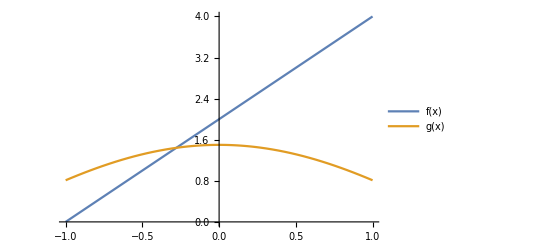

```mathematica
Plot[{f[x],g[x]},{x,-1,1},PlotLegends->"Expressions"]
```

```mathematica
Limit[f[x],x->0]
Limit[g[x],x->0]
```

2

3/2

## Limit of a sum

The limit of a sum is the sum of the limits.

```mathematica
Limit[f[x]+g[x],x->0]
```

7/2

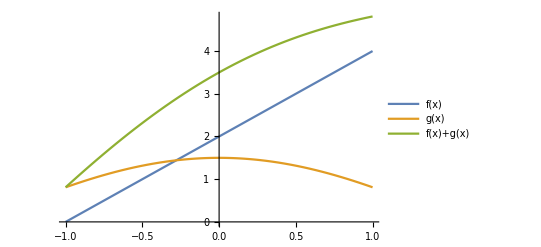

```mathematica
Plot[{f[x],g[x],f[x]+g[x]},{x,-1,1},PlotLegends->"Expressions"]
```

### Difference Law

The limit of a difference is the difference of the limits.

```mathematica
Limit[f[x]-g[x],x->0]
```

1/2

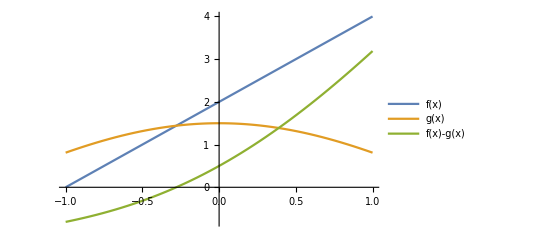

```mathematica
Plot[{f[x],g[x],f[x]-g[x]},{x,-1,1},PlotLegends->"Expressions"]
```

### Scalar Multiplication

The of a constant times a function is the constant times the limit of the function.

```mathematica
Limit[3f[x],x->0]
```

6

### Product Law

The limit of a product is the product of the limits.

```mathematica
Limit[f[x]g[x],x->0]
```

3

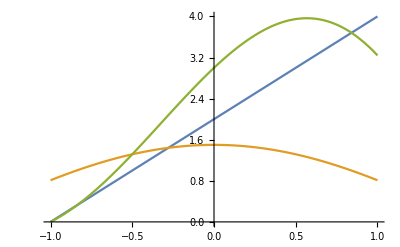

```mathematica
Plot[{f[x],g[x],f[x]*g[x]},{x,-1,1}]
```

### Power Law

The limit of a power of a function is the power of the limit of the function

```mathematica
Limit[f[x]^3,x->0]
```

8

### Quotient Law

The limit of a quotient is the quotient of the limits, if the limit of the denominator is not 0.

```mathematica
Limit[f[x]/g[x], x->0]
```

4/3

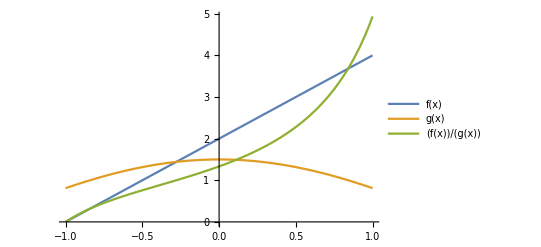

```mathematica
Plot[{f[x],g[x],f[x]/g[x]},{x,-1,1},PlotLegends->"Expressions"]
```

```mathematica
g[π/2]
```

0

```mathematica
Limit[f[x]/g[x], x->π/2]
```

Indeterminate

```mathematica
Limit[c,x->a]==c
```

True

```mathematica
Limit[x,x->a]==a
```

True

```mathematica
Limit[2 x^2-4x+3,x->4]
```

19

## Limit of a Rational Function

```mathematica
f[x_]:=(x^3-x^2+2)/(5x-3)
```

identify constituent polynomials

```mathematica
g[x_]:=x^3-x^2+2
h[x_]:=-3+5x
```

```mathematica
{Limit[f[x],x->-2],Limit[g[x],x->-2]/Limit[h[x],x->-2],f[-2]}
```

{10/13,10/13,10/13}

## Limit of a Rational Function: Special Case

Compute the limit for the following function as x approaches -1.

```mathematica
f[x_]:=(x^2-1)/(x+1)
```

The denominator equals 0 at -1, so you cannot use the quotient law:

```mathematica
x+1/.x->-1
```

0

To find the limit, factor the numerator:

```mathematica
Factor[x^2-1]
```

(-1+x) (1+x)

To cancel the common factor (1+x), use Simplify:

```mathematica
Simplify[f[x]]
```

-1+x

Therefore the limit is -2 at -1.

```mathematica
Limit[f[x],x->-1]
```

-2

## Difference Quotient

Find the limit of the following function as h approaches 0:

```mathematica
f[h_]:=((2+h)^2-4)/h
```

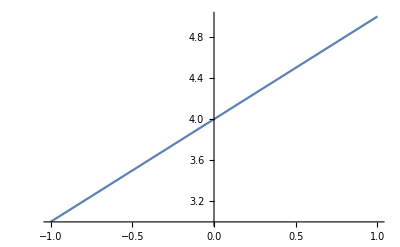

```mathematica
Plot[f[h],{h,-1,1}]
```

To spot the common factor, expand the numerator:

```mathematica
Expand[(2+h)^2-4]
```

4 h+h^2

Since h is also a factor of the denominator, cancel it:

```mathematica
Factor[f[h]]
```

4+h

Hence the limit as h approaches 0 is 4.

```mathematica
Limit[f[h],h->0]
```

4

## One-Sided Limits: Absolute Value Function

Compute the limit for the absolute value function | x | as x approaches 0:

```mathematica
f[x_]:=RealAbs[x]
```

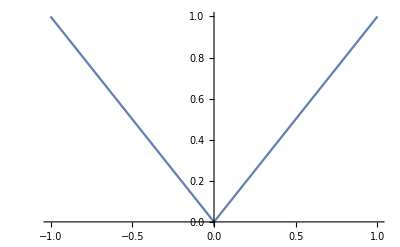

```mathematica
Plot[f[x],{x,-1,1}]
```

It is clear that the left-hand limit and right-hand limit are both 0 at 0.
Can be confirmed by using Limit function.

```mathematica
{Limit[f[x],x->0,Direction->1],
Limit[f[x],x->0,Direction->-1]}
```

{0,0}

```mathematica
Limit[f[x],x->0]
```

0

## Nonexistent Limit

```mathematica
f[x_]:=RealAbs[x]/x
```

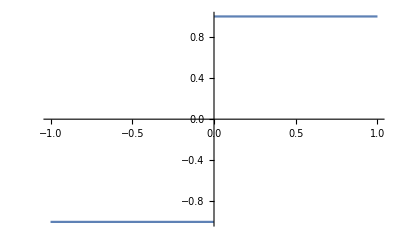

```mathematica
Plot[f[x],{x,-1,1}]
```

```mathematica
{Limit[f[x],x->0,Direction->1],
Limit[f[x], x->0,Direction->-1]}
```

{-1,1}

```mathematica
Limit[f[x],x->0]
```

Indeterminate

## Floor Function

```mathematica
f[x_]:=Floor[x]
```

Find the places where the limit does not exist in the range  from -2 to 2.

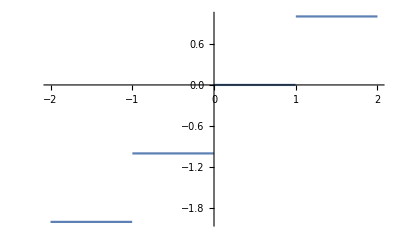

```mathematica
Plot[f[x],{x,-2,2}]
```

```mathematica
{Limit[f[x],x->0,Direction->1],
Limit[f[x],x->0,Direction->-1]}
```

{-1,0}

```mathematica
Limit[f[x],x->#]&/@Range[-2,2]
```

{Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate}

## Squeeze Theorem

```mathematica
g[x_]:=x^2Cos[1/x]
```

Squeeze theorem: if f[x]>=g[x] near a, and g[x]>=h[x] near a, and the limits of f and h at a are both L, then the limit of g at a is also L.

We choose the functions that bound g to be x^2 and -x^2.

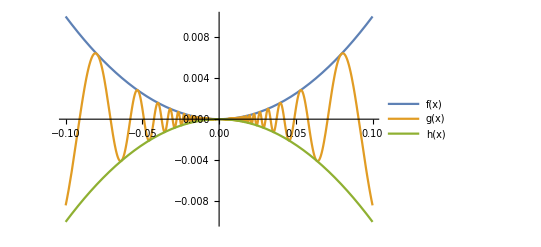

```mathematica
f[x_]:=x^2;
h[x_]:=-x^2;
Plot[{f[x],g[x],h[x]},{x,-.1,.1},PlotLegends->"Expressions"]
```

```mathematica
{Limit[f[x],x->0],
Limit[h[x],x->0]}
```

{0,0}

```mathematica
Limit[g[x],x->0]
```

0

## Exercises - Lesson 5:

## Exercise 1 - Polynomial

```mathematica
f[x_]:=x^6+3 x^2+9
```

```mathematica
f[1]
```

13

```mathematica
Limit[f[x],x->1]==13
```

True

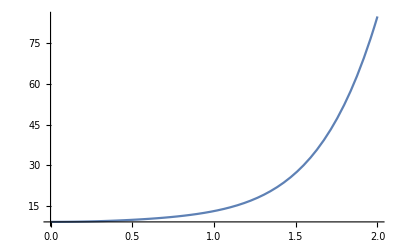

```mathematica
Plot[f[x],{x,0,2}]
```

## Exercise 2 - Limit of Sum

Find limit for function as x approaches -4:

```mathematica
f[x_]:=3x+Abs[x+4]
```

```mathematica
g[x_]:=3x
h[x_]:=Abs[x+4]
```

```mathematica
Limit[g[x],x->-4]+Limit[h[x],x->-4]
```

-12

```mathematica
Limit[f[x],x->-4]==-12
```

True

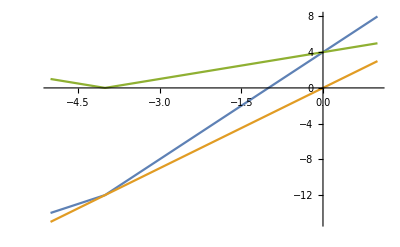

```mathematica
Plot[{f[x],g[x],h[x]},{x,-5,1}]
```

## Exercise 3 - Limit of a Product

```mathematica
f[x_]:=(x^4-5x)(3-Sqrt[x])
```

Compute the limit of the function as it approaches 2. Use the product law.

```mathematica
g[x_]:=(x^4-5x)
h[x_]:= 3-Sqrt[x]
```

```mathematica
{Limit[g[x],x->2]*Limit[h[x],x->2],
Limit[g[x],x->2]*Limit[h[x],x->2]//N}
```

{6 (3-√2),9.51472}

```mathematica
Limit[f[x],x->2]==6(3-Sqrt[2])
```

True

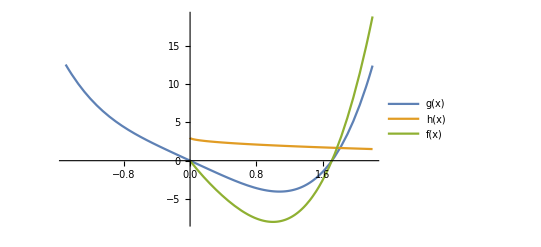

```mathematica
Plot[{g[x],h[x],f[x]},{x,-1.5,2.2},PlotLegends->"Expressions"]
```

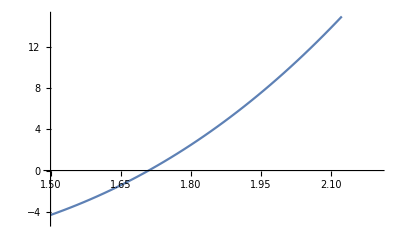

```mathematica
Plot[f[x], {x, 1.5, 2.2}, Sequence[
 PlotRange -> {-5, 15}, GridLines -> {{2}, {6 (3 - Sqrt[2])}}]]
```

## Exercise 4 - Limit of Quotient

compute the limit of the following function as it approaches 0:

```mathematica
f[x_]:=(2 x^4+5)/(7x+9)
```

```mathematica
f[0]
```

5/9

```mathematica
Limit[f[x],x->0]==5/9
```

True

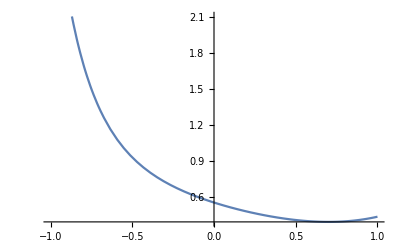

```mathematica
Plot[f[x],{x,-1,1}]
```

## Exercise 5 - Limit of a Quotient

Compute the limit of the following function as x approaches 0:

```mathematica
f[x_]:=(Sqrt[5+x]-Sqrt[5])/x
```

```mathematica
FullSimplify[f[x]]
```

1/(√5+√(5+x))

```mathematica
Trace[FullSimplify[f[x]]]
```

{{f[x],(√(5+x)-√5)/x,{{√(5+x),√(5+x)},{{√5,√5},-√5},√(5+x)-√5,-√5+√(5+x)},(-√5+√(5+x))/x,(-√5+√(5+x))/x},FullSimplify[(-√5+√(5+x))/x],1/(√5+√(5+x))}

```mathematica
Simplify[f[x]]
```

(-√5+√(5+x))/x

```mathematica
FullSimplify[f[x]]
```

1/(√5+√(5+x))

```mathematica
Limit[f[x],x->0]
```

1/(2 √5)

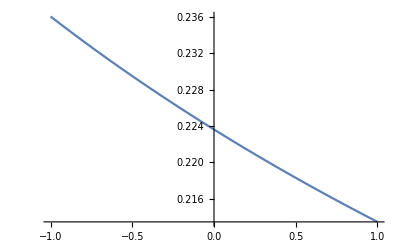

```mathematica
Plot[f[x],{x,-1,1},GridLines->{None,{1/(2Sqrt[5])}}]
```

## Exercise 6 - Squeeze Theorem

```mathematica
f[x_]:=x Sin[1/x]
```

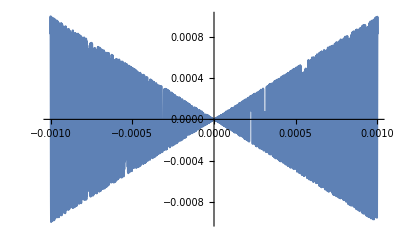

```mathematica
Plot[f[x],{x,-.001,.001}]
```

```mathematica
Limit[Sin[1/x],x->0]
```

Indeterminate

```mathematica
g[x_]:=RealAbs[x]
h[x_]:=-RealAbs[x]
```

```mathematica
{{Limit[g[x],x->0],
Limit[h[x],x->0]},
Limit[f[x],x->0]==0}
```

{{0,0},True}

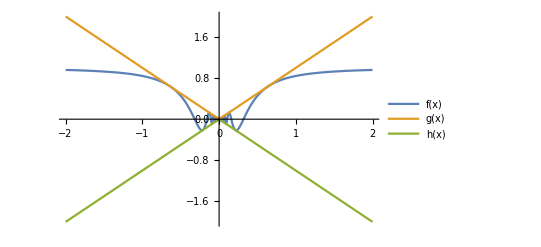

```mathematica
Plot[{f[x],g[x],h[x]},{x,-2,2},PlotLegends->"Expressions"]
```

## Final Exercise - Length Contraction

```mathematica
lorentz[v_]:=L0 Sqrt[1-v^2/c^2]
L0 =1;
c = 299792458;
```

```mathematica
Limit[lorentz[v],v->c,Direction->"FromBelow"]
```

0